## Feeding on n-prey-at-a-time Type II functional response

```mathematica
Clear["Global`*"]
SetDirectory[NotebookDirectory[]];
SetDirectory["../figs/"]
```

/Users/marknovak/Git/FR_n-prey-at-a-time/figs

### Functional response

```mathematica
s=Sum[(β x)^i,{i,1,n}]
(s/(1+s))//Simplify
```

(x β (-1+(x β)^n))/(-1+x β)

(x β (-1+(x β)^n))/(-1+(x β)^(1+n))

```mathematica
s=Sum[(β x)^i,{i,1,∞}]
(s/(1+s))//Simplify
```

-(x β)/(-1+x β)

x β

So now  substitute ' β -> a h' and ' x -> R' to get ...

#### Feeding on n prey at a time

```mathematica
S[n_]=Sum[(a h)^i R^i,{i,1,n}];
f[n_,R_]=(1/h)(S[n]/(1+S[n]))//Simplify
f[1,R]//Simplify
```

(a R (-1+(a h)^n R^n))/(-1+a h (a h)^n R^(1+n))

(a R)/(1+a h R)

#### Infinite summation gives the “Type 1” functional response

```mathematica
Sinf[n_]=Sum[(a h)^i R^i,{i,1,∞}];
finf[R_]=(1/h)(Sinf[n]/(1+Sinf[n]));
finf[R]//Simplify
```

a R

#### Illustrate

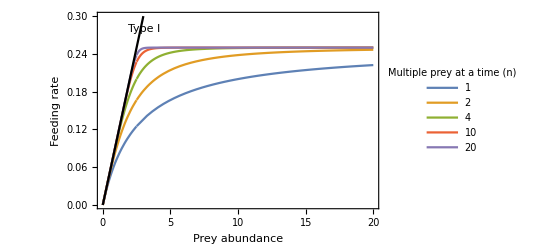

```mathematica
fparms={h-> 4,a-> 0.1};
nvals={1,2, 4, 10, 20};
prange = {{0,20},{0,0.3}};
p1=Plot[Evaluate[f[n,R]/.fparms/.n-> nvals], {R,0,20},
PlotRange->prange,
PlotLegends -> Placed[
LineLegend[nvals,
LegendLabel-> "Multiple prey at a time (n)" ,
LegendFunction->(Framed[#,RoundingRadius->5]&),
LegendMargins->0.1,
LegendLayout-> {"Row",1},
Spacings->0.15],
{Right,Bottom}],
Axes->False,Frame->{{True,False},{True,False}},
FrameLabel->{Style["Prey abundance",14],Style["Feeding rate",14]}
];
p2=Plot[finf[R]/.fparms,{R,0,20},
PlotRange->prange,
PlotStyle->{Black},
PlotLabels-> Placed[{"Type I"},Right]];
P1=Show[p1,p2]
Export["FR_n-prey-at-a-time.pdf",P1,"PDF",
"AllowRasterization"->False,ImageSize->360];
```

#### Compare to diminishing handling times

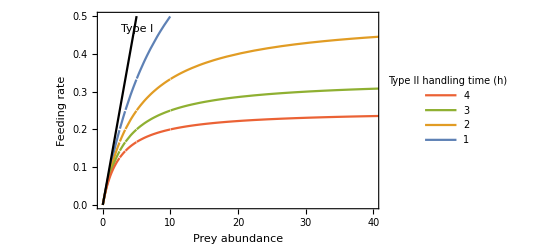

```mathematica
hvals = Table[h,{h,1,4,1}];

prange = {{0,40},{0,0.5}};
p3=Plot[Evaluate[f[1,R]/.Drop[fparms,1]/.h-> hvals], {R,0,100},
PlotRange->prange,
PlotLegends -> Placed[
LineLegend[hvals,
LegendLabel-> "Type II handling time (h)" ,
LegendFunction->(Framed[#,RoundingRadius->5]&),
LegendMargins->0.1,
LegendLayout-> {"ReversedRow",1},
Spacings->0.15],
{Right,Bottom}],
Axes->False,Frame->{{True,False},{True,False}},
FrameLabel->{Style["Prey abundance",14],Style["Feeding rate",14]}
];
p2=Plot[finf[R]/.fparms,{R,0,100},
PlotRange->prange,
PlotStyle->{Black},
PlotLabels-> Placed[{"Type I"},Right]];
P2=Show[p3,p2]
Export["FR_htime-to-zero.pdf",P2,"PDF",
"AllowRasterization"->False,ImageSize->360];
```

(a R)/(1+a h R)

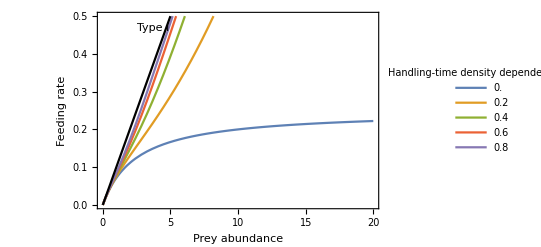

```mathematica
fT2h[R_]=(a R)/(1 + a h Exp[-(η R)] R);
fT2h[R]/.η-> 0
ηvals = Table[η,{η,0,0.8,0.2}];

prange = {{0,20},{0,0.5}};
p4=Plot[Evaluate[fT2h[R]/.fparms/.η->ηvals], {R,0,20},
PlotRange->prange,
PlotLegends -> Placed[
LineLegend[ηvals,
LegendLabel-> "Handling-time density dependence (η)" ,
LegendFunction->(Framed[#,RoundingRadius->5]&),
LegendMargins->1,
LegendLayout-> {"Row",1},
Spacings->0.15],
{Right,Bottom}],
Axes->False,Frame->{{True,False},{True,False}},
FrameLabel->{Style["Prey abundance",14],Style["Feeding rate",14]}
];
p2=Plot[finf[R]/.fparms,{R,0,20},
PlotRange->prange,
PlotStyle->{Black},
PlotLabels-> Placed[{"Type I"},{{2.5,0.45},{0,0}}]];
P3=Show[p4,p2]
Export["FR_htime_diminishing.pdf",P3,"PDF",
"AllowRasterization"->False,ImageSize->360];
```

### Given Rosenzweig-MacArthur model

```mathematica
dRdt=r R (1-R/Κ)-f[n,R]P;
dPdt=e f[n,R]P-d P;

(*Good isocline spacing over dynamical range*)
(* parms={a->0.02,r->0.5,e->0.25,d->0.08, Κ-> 100, h-> 2} *)
parms={a->0.02,r->0.5,e->0.25,d->0.08, Κ-> 100, h-> 2};
```

#### Isoclines

```mathematica
isoR[R_]=P/.Solve[dRdt==0,P]
```

{-(r (-1+a h (a h)^n R^(1+n)) (R-Κ))/(a (-1+(a h)^n R^n) Κ)}

Solving for isoP gives n solutions for n-prey-at-a-time (all but one of which are complex), so gets complicated quickly.  But isoP always remains independent of R or P.  Thus evaluate numerically and remove complex and negative values.

```mathematica
Clear[isoP]
isoP[ν_]:=Select[R/.Solve[(dPdt/.n->ν)==0,R]/.parms,Abs[Im[#]]< 10^-13&&Re[#]>0&]//Flatten
```

Values of predator isocline converge on constant very quickly

```mathematica
isoPvals=Re[isoP/@nvals]//Flatten
```

{44.4444,23.1,17.5223,16.0697,16.0008}

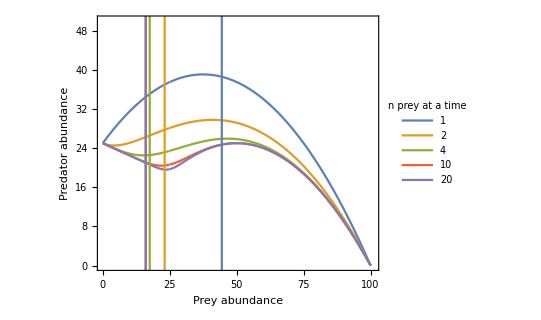

```mathematica
p4=Plot[Evaluate[isoR[R]/.parms/.n-> nvals],{R,0,100},
PlotRange->{{0,1+Κ/.parms},{0,50}},
PlotRangePadding->0,
AspectRatio->0.8,
Axes->False,Frame->{{True,True},{True,True}},
FrameLabel->{Style["Prey abundance",14],Style["Predator abundance",14]}
];
addEpilog[g_Graphics,epi_List]:=With[{styles=Cases[g[[1]],{dir__,__Line}:>Directive[dir],-5]},Show[g,Epilog->{styles,epi}~Flatten~{2}]]
p5=addEpilog[p4,InfiniteLine[{{#,0},{#,1}}]&/@isoPvals];
P4=Legended[p5,Placed[LineLegend[ColorData[97,"ColorList"][[1;;Length[nvals]]],nvals,LegendLabel-> "n prey at a time" , LegendFunction->(Framed[#,RoundingRadius->5]&),
LegendMargins->0.1,
Spacings-> 0.1],
{{0.7,0.63},{0,0}}]]
Export["Isoclines.pdf",P4,"PDF",
"AllowRasterization"->False,ImageSize->360];
```

#### Time series

```mathematica
Clear[model];
model[n_]:={
R'[t]==r R[t](1-R[t]/Κ)-(a R[t] (-1+(a h)^n (R[t])^n))/(a h (a h)^n (R[t])^(1+n)-1)P[t],
R[0]==0.1,
P'[t]==e (a R[t] (-1+(a h)^n (R[t])^n))/(a h (a h)^n (R[t])^(1+n)-1)P[t]-d P[t],
P[0]==0.1
};
```

```mathematica
Manipulate[
subparms = {a-> α,r->ρ,e->ϵ,d->δ, Κ-> κ, h-> η};Plot[Evaluate[{R[t],P[t]}/.First[NDSolve[{model[n]/.subparms},{R,P},{t,0,1000}]]],{t,0,1000},PlotRange->{0,All}],
{n,1,20,0.1},
{{α,0.02,"a"},0.001,0.1,0.001},
{{ρ,0.5,"r"},0.1,1,0.05},
{{ϵ,0.25,"e"},0.05,0.5,0.05},
{{δ,0.08,"d"},0.01,0.1,0.005},
{{κ,100,"K"},1,200,1},
{{η,2,"h"},0,5,0.05},
ControlPlacement->Left
]
```

#### Bifurcation plot with n as control parameter

```mathematica
Phighs=ParallelTable[{sol,points}=
Quiet[Reap@NDSolveValue[{model[n]/.parms,WhenEvent[P'[t]<0,
If[t>9900,Sow[P[t]]]]},{R,P},{t,0,10000}]];
{n,#}&/@Union[Flatten[points],SameTest->(Abs[#1-#2]<.0001&)],{n,0.5,13,0.01}];
Plows=ParallelTable[{sol,points}=
Quiet[Reap@NDSolveValue[{model[n]/.parms,WhenEvent[P'[t]>0,
If[t>9900,Sow[P[t]]]]},{R,P},{t,0,10000}]];
{n,#}&/@Union[Flatten[points],SameTest->(Abs[#1-#2]<.0001&)],{n,0.5,13,0.01}];
```

```mathematica
PhighsL=ParallelTable[{sol,points}=
Quiet[Reap@NDSolveValue[{model[n]/.parms,WhenEvent[P'[t]<0,
If[t>9900,Sow[P[t]]]]},{R,P},{t,0,10000}]];
{n,#}&/@Union[Flatten[points],SameTest->(Abs[#1-#2]<.0001&)],{n,0.5,1.2,0.0005}];
PlowsL=ParallelTable[{sol,points}=
Quiet[Reap@NDSolveValue[{model[n]/.parms,WhenEvent[P'[t]>0,
If[t>9900,Sow[P[t]]]]},{R,P},{t,0,10000}]];
{n,#}&/@Union[Flatten[points],SameTest->(Abs[#1-#2]<.0001&)],{n,0.5,1.2,0.0005}];
```

```mathematica
PhighsH=ParallelTable[{sol,points}=
Quiet[Reap@NDSolveValue[{model[n]/.parms,WhenEvent[P'[t]<0,
If[t>9900,Sow[P[t]]]]},{R,P},{t,0,10000}]];
{n,#}&/@Union[Flatten[points],SameTest->(Abs[#1-#2]<.0001&)],{n,11.6,13,0.0005}];
PlowsH=ParallelTable[{sol,points}=
Quiet[Reap@NDSolveValue[{model[n]/.parms,WhenEvent[P'[t]>0,
If[t>9900,Sow[P[t]]]]},{R,P},{t,0,10000}]];
{n,#}&/@Union[Flatten[points],SameTest->(Abs[#1-#2]<.0001&)],{n,11.6,13,0.0005}];
```

```mathematica
Rhighs=ParallelTable[{sol,points}=
Quiet[Reap@NDSolveValue[{model[n]/.parms,WhenEvent[R'[t]<0,
If[t>9900,Sow[R[t]]]]},{R,P},{t,0,10000}]];
{n,#}&/@Union[Flatten[points],SameTest->(Abs[#1-#2]<.0001&)],{n,0.5,13,0.01}];
Rlows=ParallelTable[{sol,points}=
Quiet[Reap@NDSolveValue[{model[n]/.parms,WhenEvent[R'[t]>0,
If[t>9900,Sow[R[t]]]]},{R,P},{t,0,10000}]];
{n,#}&/@Union[Flatten[points],SameTest->(Abs[#1-#2]<.0001&)],{n,0.5,13,0.01}];
```

```mathematica
RhighsL=ParallelTable[{sol,points}=
Quiet[Reap@NDSolveValue[{model[n]/.parms,WhenEvent[R'[t]<0,
If[t>9900,Sow[R[t]]]]},{R,P},{t,0,10000}]];
{n,#}&/@Union[Flatten[points],SameTest->(Abs[#1-#2]<.0001&)],{n,0.5,1.2,0.001}];
RlowsL=ParallelTable[{sol,points}=
Quiet[Reap@NDSolveValue[{model[n]/.parms,WhenEvent[R'[t]>0,
If[t>9900,Sow[R[t]]]]},{R,P},{t,0,10000}]];
{n,#}&/@Union[Flatten[points],SameTest->(Abs[#1-#2]<.0001&)],{n,0.5,1.2,0.001}];
```

```mathematica
RhighsH=ParallelTable[{sol,points}=
Quiet[Reap@NDSolveValue[{model[n]/.parms,WhenEvent[R'[t]<0,
If[t>9900,Sow[R[t]]]]},{R,P},{t,0,10000}]];
{n,#}&/@Union[Flatten[points],SameTest->(Abs[#1-#2]<.0001&)],{n,11.6,13,0.0005}];
RlowsH=ParallelTable[{sol,points}=
Quiet[Reap@NDSolveValue[{model[n]/.parms,WhenEvent[R'[t]>0,
If[t>9900,Sow[R[t]]]]},{R,P},{t,0,10000}]];
{n,#}&/@Union[Flatten[points],SameTest->(Abs[#1-#2]<.0001&)],{n,11.6,13,0.0005}];
```

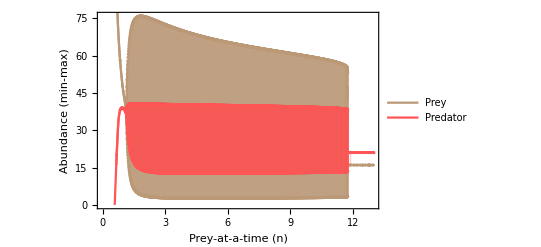

```mathematica
p5=ListPlot[{Flatten[Phighs,1],Flatten[Plows,1]},
Filling->{1->{2}},
PlotRange->{{0,Full},{0,Full}},
PlotStyle->Lighter[Red],
Axes->False,Frame->{{True,False},{True,False}}];

p6=ListPlot[{Flatten[PhighsL,1],Flatten[PlowsL,1]},
Filling->{1->{2}},
Joined-> True,
PlotStyle->Lighter[Red],
PlotRange->{{0,1.2},{0,Full}}];

p7=ListPlot[{Flatten[PhighsH,1],Flatten[PlowsH,1]},
Filling->{1->{2}},
Joined-> True,
PlotStyle->Lighter[Red],
PlotRange->{{11.6,12},{0,Full}}];

p8=ListPlot[{Flatten[Rhighs,1],Flatten[Rlows,1]},
Filling->{1->{2}},
PlotStyle->Lighter[Brown],
PlotRange->{{0,Full},{0,Full}},
Axes->False,Frame->{{True,False},{True,False}},
FrameLabel->{Style["Prey-at-a-time (n)",14],Style["Abundance\n(min-max)",14]}];

p9=ListPlot[{Flatten[RhighsL,1],Flatten[RlowsL,1]},
Filling->{1->{2}},
Joined-> True,
PlotStyle->Lighter[Brown],
PlotRange->{{0,1.2},{0,Full}}];

p10=ListPlot[{Flatten[RhighsH,1],Flatten[RlowsH,1]},
Filling->{1->{2}},
Joined-> True,
PlotStyle->Lighter[Brown],
PlotRange->{{11.6,12},{0,Full}}];

P5=Legended[Show[p8,p9,p10,p5,p6,p7],Placed[LineLegend[{Lighter[Brown],Lighter[Red]},{"Prey","Predator"},
 LegendFunction->(Framed[#,RoundingRadius->5]&),
LegendMargins->0.1,
Spacings-> 0.1],
{{0.7,0.76},{0,0}}]]
Export["Bifurcation.pdf",P5,"PDF",
"AllowRasterization"->False,ImageSize->360];
```